Represent a graph as a list of it nodes, each node a list {m_i,{n_j1,n_j2,n_jN},ϕ_i}; with m_j∈ℕ^+ an integer (the amount of marbles at node m); {n_j1,n_j2,n_jN} the list of neighbors of node m; and ϕ_j the phase that determines if marbles are able to leave the node or not. When ϕ_j==0 or Sin[ω t+ϕ_i]≥ 0 marbles can leave the node.
Given a network, the rules of the simulation are that at every tick:
	■ Every node passes one of its marbles to one of its neighbors. The marble is passed if ϕ_j∨Sin[ω t+ϕ_i]≥ 0, otherwise the marble stays. The marble goes to one of the node’s neighbor with equal probability.

graphToNet[graph, fun] takes a graph (Mathematica style) and returns a list {{m_1,{n_11,n_12,n_(1 N_1)},ϕ_1},…,{m_i,{n_(j 1),n_(j 2),n_(j N_j)},ϕ_j},…,{m_N,{n_(N 1),n_(N 2),n_(N N_N)},ϕ_N}}; with N the number of nodes in the graph, n_(j s) the s-th neighbour of node j, m_j∈[1,N] an integer, and ϕ_j determined by fun. 
By default fun is RandomChoice[{9/10,1/20,1/20}→{0,π,2π}]

```mathematica
graphToNet[g_Graph,ϕ_:(RandomChoice[{9/10,1/20,1/20}->{0,π,2π}]&)]:=Module[{nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]],n=VertexCount[g]},
{RandomInteger[n],#,ϕ[]}&/@nei
]
```

netEvolve[graph, ω,T] takes a graph (represented as previously described), with N nodes, an integer T, and a real ω and implements the rule described above for T ticks. It returns an M×T matrix where every row has the number of marbles  of its corresponding node for each tick. This is, element e_(m,t) is the number of marbles of node m at tick t.

netEvolveTrace[graph, ω,T] does the same as netEvolve, but it returns a list {{{s_11,…,s_N1},…,{s_(1T),…,s_(N T)}}},E} with s_(n t) the number of the node that received the marble from node n at time t.

```mathematica
ω=1/2;
```

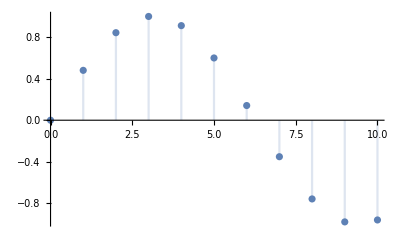

```mathematica
DiscretePlot[Sin[ω t], {t,0,10}]
```

```mathematica
netEvolve[graph_List,ω_Real?Positive,T_Integer]:=Module[
{output={graph},nodes=Length[graph],add,remove,t,tmp},
remove[node:{0,neighs_,ϕ_}]:=node;
remove[node:{m_,neighs_,0}]:={{m-1,neighs,0},RandomChoice[neighs]};
remove[node:{m_,neighs_,ϕ_}]:=If[Sin[ω t+ϕ]<0,node,{{m-1,neighs,ϕ},RandomChoice[neighs]}];
t=0;
add=remove/@graph (*remove marble at each node, note where it goes*);
tmp=Cases[add,{_List,i_}->i](*get the destination nodes*);
add=add/.{node_List,i_Integer}->node(*clean the network*);
tmp={#,Count[tmp,#]}&/@Union[tmp](*count how many marbles go to each node*);
tmp=({#[[1]],1}->add[[#[[1]],1]]+#[[2]])&/@tmp(*build rules to add marbles*);
AppendTo[output,ReplacePart[add,tmp]](*add marbles*);
For[t=1,t<T,t++,
(*Print[{remove[graph[[1]]],Sin[ω t+graph[[1,3]]]}]*)
add=remove/@output[[-1]] (*remove marble at each node, note where it goes*);
tmp=Cases[add,{_List,i_}->i](*get the destination nodes*);
add=add/.{node_List,i_Integer}->node(*clean the network*);
tmp={#,Count[tmp,#]}&/@Union[tmp](*count how many marbles go to each node*);
tmp=({#[[1]],1}->add[[#[[1]],1]]+#[[2]])&/@tmp(*build rules to add marbles*);
AppendTo[output,ReplacePart[add,tmp]](*add marbles*);
];
output[[All,All,1]]
]
```

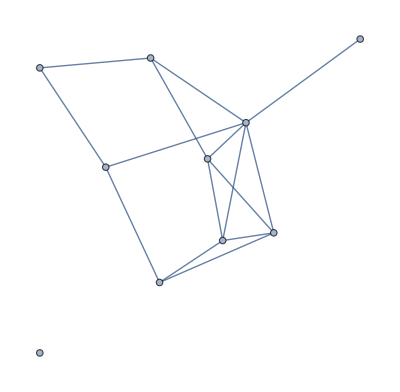

```mathematica
gr=RandomGraph[{10,15}]
```

```mathematica
test=graphToNet[gr]
```

{{10,{3,4,6,8},0},{2,{4},0},{1,{1,4,9},0},{4,{1,2,3,6,8,10},0},{0,{6,8,10},0},{4,{1,4,5,8},0},{0,{},2 π},{10,{1,4,5,6},0},{0,{3,10},0},{9,{4,5,9},0}}

```mathematica
marbles=netEvolve[test,.5,50];
```

Para mirar el número de pelotas en cada nodo (ejemplo con el nodo 4):

```mathematica
marbles[[All,4]]
```

{4,5,5,5,6,7,7,7,6,5,7,6,6,7,7,7,7,7,7,7,7,8,9,11,10,9,10,11,10,11,12,12,12,11,13,13,13,13,14,14,13,12,13,12,12,14,14,14,14,14,13}

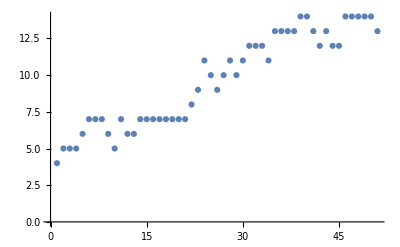

```mathematica
ListPlot[marbles[[All,4]]]
```

El 7, que está solo, permanece constante

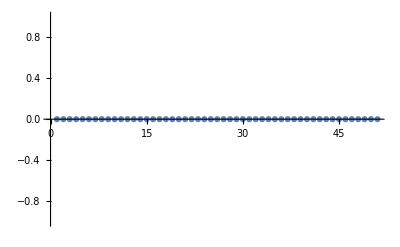

```mathematica
ListPlot[marbles[[All,7]]]
```

El número total de pelotas es

```mathematica
Total/@marbles
```

{40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40}

La densidad de nodos en un tick (el último)

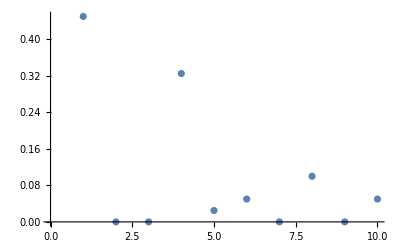

```mathematica
ListPlot[marbles[[-1]]/Total[marbles[[-1]]]]
```

La densidad de nodos en el tiempo

```mathematica
ListPlot3D[marbles/Total[marbles[[-1]]],AxesLabel->{"Node","time",ρ}]
```

-Graphics3D-